```mathematica
u = BesselJ[0,6.306437047688424x]-(BesselJ[0, 6.306437047688424]/BesselI[0, 6.306437047688424])BesselI[0,6.306437047688424x]
```

-0.00253015 BesselI[0,6.30644 x]+BesselJ[0,6.30644 x]

```mathematica
Minimize[D[u, x],{x} ∈Interval[{0,1}]]
Maximize[D[u, x],{x} ∈Interval[{0,1}]]
Maximize[Abs[D[u, x]],{x} ∈Interval[{0,1}]]
```

{-3.69144,{x→0.293234}}

{1.70222,{x→0.815103}}

{3.69144,{x→0.293234}}

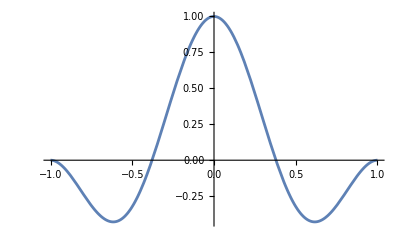

```mathematica
Plot[u,{x, -1, 1}]
```

```mathematica
f[x_, k_]=BesselJ[k, x]BesselI[k+1,x]+BesselI[k,x]BesselJ[k+1,x];
(roots = NSolve[{f[x, 6]==0, 0 < x <= 40}, x, Reals]) // N
```

{{x→10.687},{x→14.3552},{x→17.7764},{x→21.0971},{x→24.3647},{x→27.6003},{x→30.8149},{x→34.015},{x→37.2045}}

```mathematica
{{x->10.687025855471223},{x->14.35515633662993},{x->17.776433783116655},{x->21.09712080854162},{x->24.364701717219408},{x->27.600280820827404},{x->30.81490499738921},{x->34.01498921852601},{x->37.20454026962541}}
```